```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/

## Input

```mathematica
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[2,{2}]}->{F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/equivalence_classes.m

## Diagrams generation

## Topologies

### Born

```mathematica
topologiesBorn=CreateTopologies[0,1->1,ExcludeTopologies->{Tadpoles,WFCorrections}];
Print["Number of topologies: ",{topologiesBorn}//Map[Length]]
```

Number of topologies: {0}

```mathematica
Paint[topologiesBorn];
Print["Number of topologies: ",topologiesBorn//Length]
```

Number of topologies: 0

### 1-Loop

```mathematica
topologies1L=CreateTopologies[1,1->1,ExcludeTopologies->{Tadpoles,WFCorrections}];
Print["Number of topologies: ",{topologies1L}//Map[Length]]
```

Number of topologies: {2}

#### Paint

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

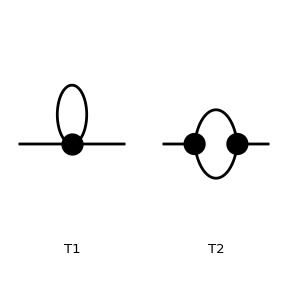

```mathematica
Paint[topologies1L,ColumnsXRows->{2,1}];
```

## Insert Fields

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

### Born

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
Print["Number of diagrams: ",fieldsBorn//Length]
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 344 counterterms of order 1

> 26 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

Restoring 24 field point(s)

in total: 0 Particles insertions

Number of diagrams: 0

#### Paint

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

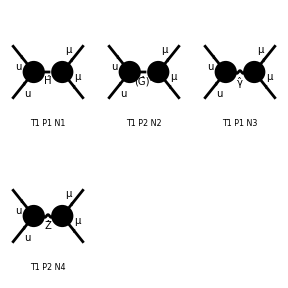

```mathematica
Paint[fieldsBorn];
```

### 1-Loop

```mathematica
fields1L=InsertFields[topologies1L, process];
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 6 Particles insertions

Restoring 24 field point(s)

in total: 6 Particles insertions

#### Paint

> Top. 1 ac/bd/cdcd.m, 0 diagrams

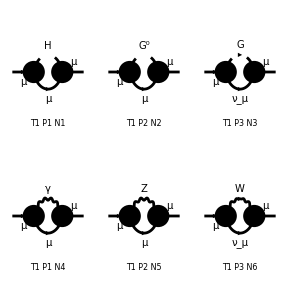

```mathematica
Paint[fields1L];
```

## Diagram Backup

## Save

```mathematica
fieldsBorn>>(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L>>(NotebookDirectory[]<>"backup/fields/fields1L.m");
```

## Load

```mathematica
fieldsBorn=<<(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L=<<(NotebookDirectory[]<>"backup/fields/fields1L.m");
```

### Paint

```mathematica
Paint[fields1L];
```

> Top. 1 ac/bd/cdcd.m, 0 diagrams

-Graphics-

## Projection

## Amplitudes

```mathematica
amp1L=CreateFeynAmp[fields1L,GaugeRules->{}]
myAmp1L=ExtractAmplitude[amp1L];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 344 counterterms of order 1

> 26 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

in total: 6 Particles amplitudes

FeynAmpList[Process→{{F[2,{2}],p1,MM,{Ql,LeptonNumber}}}→{{F[2,{2}],k1,MM,{Ql,LeptonNumber}}},Model→{SMbgf_Anglerfish},GenericModel→{Lorentzbgf},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[q1],ⅈ (2 π)^-d ū[k1,MM].(ⅈ EL gHll MM om_-+ⅈ EL gHll MM om_+).(MM+gs[q1]).(ⅈ EL gHll MM om_-+ⅈ EL gHll MM om_+).u[p1,MM] FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(-MH^2+(q1-k1)^2)]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==2,Number==2],Integral[q1],ⅈ (2 π)^-d ū[k1,MM].(-EL gXll MM om_-+EL gXll MM om_+).(MM+gs[q1]).(-EL gXll MM om_-+EL gXll MM om_+).u[p1,MM] FeynAmpDenominator[1/(-MM^2+(q1)^2),1/((q1-k1)^2-MZ^2 xi_Q)]],FeynAmp[GraphID[Topology==1,Generic==1,Particles==3,Number==3],Integral[q1],ⅈ (2 π)^-d ū[k1,MM].(-ⅈ EL gFll MM om_-).gs[q1].(-ⅈ EL gFll MM om_+).u[p1,MM] FeynAmpDenominator[1/(q1)^2,1/((q1-k1)^2-MW^2 xi_Q)]],FeynAmp[GraphID[Topology==1,Generic==2,Particles==1,Number==4],Integral[q1],-ⅈ (2 π)^-d ū[k1,MM].(ⅈ EL gAl ga[Lor2].om_-+ⅈ EL gAl ga[Lor2].om_+).(MM+gs[q1]).(ⅈ EL gAl ga[Lor1].om_-+ⅈ EL gAl ga[Lor1].om_+).u[p1,MM] (FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(q1-k1)^2,1/(q1-k1)^2] (q1-k1)[Lor1] (-(q1)+k1)[Lor2] (1-xi_Q)+FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(q1-k1)^2] g[Lor1,Lor2])],FeynAmp[GraphID[Topology==1,Generic==2,Particles==2,Number==5],Integral[q1],-ⅈ (2 π)^-d ū[k1,MM].(ⅈ EL gZlL ga[Lor2].om_-+ⅈ EL gZlR ga[Lor2].om_+).(MM+gs[q1]).(ⅈ EL gZlL ga[Lor1].om_-+ⅈ EL gZlR ga[Lor1].om_+).u[p1,MM] (FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(-MZ^2+(q1-k1)^2),1/((q1-k1)^2-MZ^2 xi_Q)] (q1-k1)[Lor1] (-(q1)+k1)[Lor2] (1-xi_Q)+FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(-MZ^2+(q1-k1)^2)] g[Lor1,Lor2])],FeynAmp[GraphID[Topology==1,Generic==2,Particles==3,Number==6],Integral[q1],-ⅈ (2 π)^-d ū[k1,MM].(ⅈ EL gWlN ga[Lor2].om_-).gs[q1].(ⅈ EL gWNl ga[Lor1].om_-).u[p1,MM] (FeynAmpDenominator[1/(q1)^2,1/(-MW^2+(q1-k1)^2),1/((q1-k1)^2-MW^2 xi_Q)] (q1-k1)[Lor1] (-(q1)+k1)[Lor2] (1-xi_Q)+FeynAmpDenominator[1/(q1)^2,1/(-MW^2+(q1-k1)^2)] g[Lor1,Lor2])]]

```mathematica
SaveAmplitudes[myAmp1L,OutputName->"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/feynArts_amplitudes/OneLoopAmplitudes.m

## Amplitude Backup

```mathematica
myAmp1L=<<(NotebookDirectory[]<>"feynArts_amplitudes/OneLoopAmplitudes.m");
```

## Interference

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/equivalence_classes.m

We want an estimate of the computational time

1
 |  |  |  |

### Paint

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 344 counterterms of order 1

> 26 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

> Top. 1 ac/bd/cdcd.m, 0 diagrams

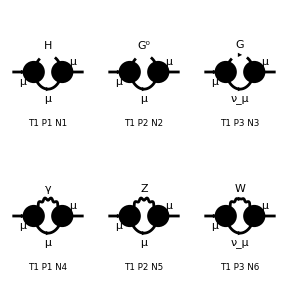

```mathematica
Paint[fields1L, ColumnsXRows->{3,2}];
```

### Mass Options

```mathematica
zeroMass={mu->0,md->0,ms->0,me->0,mm->0};
SetZeroMassParticles[zeroMass]
```

```mathematica
naturalMass={};
SetZeroMassParticles[naturalMass]
```

### Projections

```mathematica
projectorR=I*FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing,1],MM]],
NonCommutative[DiracSlash[FourMomentum[Incoming, 1]], ChiralityProjector[1]],NonCommutative[DiracSpinor[FourMomentum[Incoming,1],MM]]]
projectorL=I*FermionChain[NonCommutative[DiracSpinor[FourMomentum[Outgoing,1],MM]],
NonCommutative[DiracSlash[FourMomentum[Incoming, 1]], ChiralityProjector[-1]],NonCommutative[DiracSpinor[FourMomentum[Incoming,1],MM]]]
projector={projectorL,projectorR};
```

ⅈ DiracSpinor[k1,MM].(DiracSlash[p1].ChiralityProjector[1]).DiracSpinor[p1,MM]

ⅈ DiracSpinor[k1,MM].(DiracSlash[p1].ChiralityProjector[-1]).DiracSpinor[p1,MM]

```mathematica
SquareSimplifyAndSave[ I myAmp1L,-projector/psq^2]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_1_1.m.

ABISS: Computed contribution 1-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_1_2.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_2_1.m.

ABISS: Computed contribution 2-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_2_2.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_3_1.m.

ABISS: Computed contribution 3-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_3_2.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_4_1.m.

ABISS: Computed contribution 4-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_4_2.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_5_1.m.

ABISS: Computed contribution 5-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_5_2.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_6_1.m.

ABISS: Computed contribution 6-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm//interferences/Contribution_6_2.m.

## Squared Matrix Element Backup

```mathematica
sm=Table[<<(NotebookDirectory[]<>"interferences/Contribution_"<>ToString[i]<>"_"<>ToString[j]<>".m"),{j,2},{i,6}];
```

#### Self Energy computations

```mathematica
sprules={psq->x,SP[p1,q1]->y};
```

```mathematica
smderived=Map[smd[#,sprules,p1]&,sm,{2}];
```

```mathematica
se=(sm+smderived)//Simplify;
```

```mathematica
Do[
se[[j,i]]>>(NotebookDirectory[]<>"interferences/Contribution_"<>ToString[i]<>"_"<>ToString[j]<>".m")
,{j,2},{i,6}]
```

```mathematica
sm[[2,5]]
```

1/2 (PropList[KiraPropagator[q1,mm],KiraPropagator[-p1+q1,mz √GaugeXi[Q]]] (-(ⅈ 2^(2-d) EL^2 gZlL gZlR mm^2 π^-d)/mz^2-(ⅈ 2^(1-d) EL^2 π^-d (gZlL^2 mm^2-4 gZlL gZlR mm^2+gZlR^2 psq) SPList[SP[p1,q1]])/(mz^2 psq)+(ⅈ 2^(2-d) EL^2 π^-d (gZlL^2 mm^2-gZlL gZlR mm^2+gZlR^2 psq) SPList[SP[q1,q1]])/(mz^2 psq)-(ⅈ 2^(1-d) EL^2 π^-d (gZlL^2 mm^2+gZlR^2 psq) SPList[SP[p1,q1],SP[q1,q1]])/(mz^2 psq^2))+PropList[KiraPropagator[q1,mm],KiraPropagator[-p1+q1,mz]] ((ⅈ 2^(2-d) EL^2 gZlL gZlR mm^2 π^-d (-d mz^2+psq))/(mz^2 psq)+(ⅈ 2^(1-d) EL^2 π^-d (-4 gZlL gZlR mm^2 psq+gZlL^2 mm^2 ((-2+d) mz^2+psq)+gZlR^2 psq ((-2+d) mz^2+psq)) SPList[SP[p1,q1]])/(mz^2 psq^2)-(ⅈ 2^(2-d) EL^2 π^-d (gZlL^2 mm^2-gZlL gZlR mm^2+gZlR^2 psq) SPList[SP[q1,q1]])/(mz^2 psq)+(ⅈ 2^(1-d) EL^2 π^-d (gZlL^2 mm^2+gZlR^2 psq) SPList[SP[p1,q1],SP[q1,q1]])/(mz^2 psq^2)))

```mathematica
a=Coefficient[sm[[2,5]],PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √GaugeXi[Q]]]]//Simplify
```

0

```mathematica
b=smd[a,sprules,p1]
```

-1/(mz^2 psq)ⅈ EL^2 gZlR^2 ((2 π)^-d PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √GaugeXi[Q]]] (psq SPList[SP[p1,q1]]-SPList[SP[p1,q1],SP[q1,q1]])-2^(1-d) π^-d PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √GaugeXi[Q]],KiraPropagator[-p1+q1,mz √GaugeXi[Q]]] (psq-SPList[SP[p1,q1]]) (psq SPList[SP[p1,q1]]-2 psq SPList[SP[q1,q1]]+SPList[SP[p1,q1],SP[q1,q1]]))

```mathematica
Coefficient[b*psq,psq,0]
```

-1/mz^2 ⅈ EL^2 gZlR^2 (-(2 π)^-d PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √GaugeXi[Q]]] SPList[SP[p1,q1],SP[q1,q1]]+2^(1-d) π^-d PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √GaugeXi[Q]],KiraPropagator[-p1+q1,mz √GaugeXi[Q]]] SPList[SP[p1,q1],SP[p1,q1],SP[q1,q1]])

```mathematica
ShiftToIntegralFamily[sm[[2,5]]]
```

{{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √GaugeXi[Q]]],{q1→p1+q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz]],{q1→p1+q1}}}

```mathematica
??ShiftExpression
```

```mathematica
a=(ShiftExpression[sm[[2,5]]])//Simplify
```

1/(mz^2 psq)ⅈ EL^2 gZlR^2 (2 π)^-d (PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0]] (psq SPList[SP[q1,q1]]-2 SPList[SP[p1,q1],SP[p1,q1]]-SPList[SP[p1,q1],SP[q1,q1]])+PropList[KiraPropagator[q1,mz],KiraPropagator[p1+q1,0]] (-2 mz^2 psq+d mz^2 psq+(-2+d) mz^2 SPList[SP[p1,q1]]-psq SPList[SP[q1,q1]]+2 SPList[SP[p1,q1],SP[p1,q1]]+SPList[SP[p1,q1],SP[q1,q1]]))

```mathematica
GenerateKiraInput[]
```

```mathematica
GenerateKiraInput[SPList[SP[p1,p1]]]
```

psq userIntegral[A1,{0},0,0]

```mathematica
GenerateKiraInput[SPList[SP[q1,p1]]]
```

-1/2 userIntegral[A1,{0},-1,0]+1/2 userIntegral[A1,{0},0,-1]-1/2 psq userIntegral[A1,{0},0,0]

```mathematica
GenerateKiraInput[SPList[SP[q1,q1]]PropList[KiraPropagator[q1,mz]]]
```

userIntegral[A2,{mz},0,0]+mz^2 userIntegral[A2,{mz},1,0]

```mathematica
GenerateKiraInput[SPList[SP[q1,q1]]]
```

userIntegral[A1,{0},-1,0]

```mathematica
b=smd[1/(mz^2 psq)ⅈ EL^2 gZlR^2 (2 π)^-d (PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0]] (psq SPList[SP[q1,q1]]-2 SPList[SP[p1,q1],SP[p1,q1]]-SPList[SP[p1,q1],SP[q1,q1]])),sprules,p1]
```

1/(mz^2 psq)ⅈ EL^2 gZlR^2 (2 π)^(-2 d) ((2 π)^d PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0]] SPList[SP[p1,q1],SP[q1,q1]]-2^(1+d) π^d PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0],KiraPropagator[p1+q1,0]] (psq^2 SPList[SP[q1,q1]]-2 psq SPList[SP[p1,q1],SP[p1,q1]]-2 SPList[SP[p1,q1],SP[p1,q1],SP[p1,q1]]-SPList[SP[p1,q1],SP[p1,q1],SP[q1,q1]]))

```mathematica
Expand[c]
```

-1/mz^2 ⅈ 2^(1-d) EL^2 gZlR^2 π^-d psq PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0],KiraPropagator[p1+q1,0]] SPList[SP[q1,q1]]+1/mz^2 ⅈ 2^(2-d) EL^2 gZlR^2 π^-d PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0],KiraPropagator[p1+q1,0]] SPList[SP[p1,q1],SP[p1,q1]]+(ⅈ EL^2 gZlR^2 (2 π)^-d PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0]] SPList[SP[p1,q1],SP[q1,q1]])/(mz^2 psq)+1/(mz^2 psq)ⅈ 2^(2-d) EL^2 gZlR^2 π^-d PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0],KiraPropagator[p1+q1,0]] SPList[SP[p1,q1],SP[p1,q1],SP[p1,q1]]+1/(mz^2 psq)ⅈ 2^(1-d) EL^2 gZlR^2 π^-d PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0],KiraPropagator[p1+q1,0]] SPList[SP[p1,q1],SP[p1,q1],SP[q1,q1]]

```mathematica
c=(b/.Pi->myPi//Simplify)/.myPi->Pi
```

-1/(mz^2 psq)ⅈ EL^2 gZlR^2 (2 π)^-d (-PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0]] SPList[SP[p1,q1],SP[q1,q1]]+2 PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[p1+q1,0],KiraPropagator[p1+q1,0]] (psq^2 SPList[SP[q1,q1]]-2 psq SPList[SP[p1,q1],SP[p1,q1]]-2 SPList[SP[p1,q1],SP[p1,q1],SP[p1,q1]]-SPList[SP[p1,q1],SP[p1,q1],SP[q1,q1]]))

```mathematica
GenerateKiraInput[a]
```

-(ⅈ 2^(-1-2 d) EL^2 gZlR^2 π^(-2 d) (2^(1+d) π^d-(2 π)^d) userIntegral[A2,{mz},0,0])/(mz^2 psq)-(ⅈ 2^(-1-d) EL^2 gZlR^2 π^-d ((-2+d) mz^2+psq) userIntegral[A2,{mz},0,1])/(mz^2 psq)+(ⅈ 2^(-1-d) EL^2 gZlR^2 π^-d userIntegral[A2,{mz},1,-1])/(mz^2 psq)-(ⅈ 2^(-1-2 d) EL^2 gZlR^2 π^(-2 d) (mz^2 (2^(1+d) π^d-(-1+d) (2 π)^d)+2^(1+d) π^d psq) userIntegral[A2,{mz},1,0])/(mz^2 psq)-(ⅈ 2^(-1-d) EL^2 gZlR^2 π^-d (mz^2-psq) ((-2+d) mz^2+psq) userIntegral[A2,{mz},1,1])/(mz^2 psq)+(ⅈ 2^(-1-2 d) EL^2 gZlR^2 π^(-2 d) (2^(1+d) π^d-(2 π)^d) userIntegral[A2,{mz √GaugeXi[Q]},0,0])/(mz^2 psq)+(ⅈ 2^(-1-d) EL^2 gZlR^2 π^-d userIntegral[A2,{mz √GaugeXi[Q]},0,1])/mz^2-(ⅈ 2^(-1-d) EL^2 gZlR^2 π^-d userIntegral[A2,{mz √GaugeXi[Q]},1,-1])/(mz^2 psq)+(ⅈ 2^(-1-2 d) EL^2 gZlR^2 π^(-2 d) (2^(1+d) π^d psq+mz^2 (2^(1+d) π^d-(2 π)^d) GaugeXi[Q]) userIntegral[A2,{mz √GaugeXi[Q]},1,0])/(mz^2 psq)+(ⅈ 2^(-1-d) EL^2 gZlR^2 π^-d (-psq+mz^2 GaugeXi[Q]) userIntegral[A2,{mz √GaugeXi[Q]},1,1])/mz^2

```mathematica
Coefficient[GenerateKiraInput[b/.ShiftToIntegralFamily[b]]/.Pi->myPi,userIntegral[A2,{mz √GaugeXi[Q]},1,0]]//Simplify
```

{-(ⅈ 2^(-1-d) EL^2 gZlR^2 myPi^-d (psq+mz^2 GaugeXi[Q]))/(mz^2 psq)}

```mathematica
GenerateKiraInput[SPList[SP[p1,q1]]PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[q1+p1,0]]]
```

-1/2 userIntegral[A2,{mz √GaugeXi[Q]},0,1]+1/2 userIntegral[A2,{mz √GaugeXi[Q]},1,0]+1/2 (-psq-mz^2 GaugeXi[Q]) userIntegral[A2,{mz √GaugeXi[Q]},1,1]

```mathematica
GenerateKiraInput[SPList[SP[q1,q1]]PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[q1+p1,0]]]
```

userIntegral[A2,{mz √GaugeXi[Q]},1,1]+mz^2 GaugeXi[Q] userIntegral[A2,{mz √GaugeXi[Q]},2,1]

```mathematica
GenerateKiraInput[SPList[SP[q1,q1]]PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[q1+p1,0]]]
```

userIntegral[A2,{mz √GaugeXi[Q]},1,1]+mz^2 GaugeXi[Q] userIntegral[A2,{mz √GaugeXi[Q]},2,1]

```mathematica
GenerateKiraInput[psq PropList[KiraPropagator[q1,mz √GaugeXi[Q]],KiraPropagator[q1+p1,0]]]
```

psq userIntegral[A2,{mz √GaugeXi[Q]},1,1]

```mathematica
GenerateKiraInput[SPList[SP[q1,q1]]]
```

userIntegral[A1,{0},-1,0]

```mathematica
GenerateKiraInput[SPList[SP[q1,q1],SP[q1,p1]]]
```

-1/2 userIntegral[A1,{0},-2,0]+1/2 userIntegral[A1,{0},-1,-1]-1/2 psq userIntegral[A1,{0},-1,0]

```mathematica
GenerateKiraInput[SPList[SP[p1,q1],SP[q1,p1]]]
```

1/4 userIntegral[A1,{0},-2,0]-1/2 userIntegral[A1,{0},-1,-1]+1/2 psq userIntegral[A1,{0},-1,0]+1/4 userIntegral[A1,{0},0,-2]-1/2 psq userIntegral[A1,{0},0,-1]+1/4 psq^2 userIntegral[A1,{0},0,0]

## Shift

## Squared Matrix Element Backup

```mathematica
sm=Table[<<(NotebookDirectory[]<>"interferences/Contribution_"<>ToString[i]<>"_"<>ToString[j]<>".m"),{j,2},{i,6}];
```

## Shift

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/equivalence_classes.m

### Shift check

```mathematica
l=34;
ShiftToIntegralFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
```

Part::partw: Part \!\(\*RowBox[{"34"}]\) of \!\(\*RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{"0", ",", "0", ",", "0", ",", FractionBox[RowBox[{"\[ImaginaryI]", " ", RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}]}], "psq"], ",", RowBox[{"-", FractionBox[RowBox[{"\[ImaginaryI]", " ", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{"2", " ", "\[Pi]"}], ")"}], RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"KiraPropagator", "[", RowBox[{"q1", ",", "0"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], ")"}]}], "+", RowBox[{"\[LeftSkeleton]", "6", "\[RightSkeleton]"}], "+", RowBox[{SuperscriptBox["2", RowBox[{"1", "+", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}]], " ", RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "+", RowBox[{"SPList", "[", RowBox[{RowBox[{"SP", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"SP", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], ")"}]}]}], ")"}]}], RowBox[{SuperscriptBox["mz", "2"], " ", "psq"}]]}], ",", RowBox[{"-", FractionBox[RowBox[{"\[ImaginaryI]", " ", SuperscriptBox["EL", "2"], " ", "gWlN", " ", "gWNl", " ", RowBox[{"(", RowBox[{RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{"2", " ", "\[Pi]"}], ")"}], RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"KiraPropagator", "[", RowBox[{"q1", ",", "0"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], ")"}]}], "+", RowBox[{"\[LeftSkeleton]", "6", "\[RightSkeleton]"}], "+", RowBox[{SuperscriptBox["2", RowBox[{"1", "+", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}]], " ", SuperscriptBox["\[Pi]", RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"KiraPropagator", "[", RowBox[{"q1", ",", "0"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", "mw"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", "mw"}], "]"}]}], "]"}], " ", RowBox[{"(", RowBox[{"psq", "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], ")"}], " ", RowBox[{"(", RowBox[{RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"2", " ", "psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "+", RowBox[{"SPList", "[", RowBox[{RowBox[{"SP", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"SP", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], ")"}]}]}], ")"}]}], RowBox[{SuperscriptBox["mw", "2"], " ", "psq"}]]}]}], "}"}], ",", RowBox[{"{", RowBox[{"0", ",", "0", ",", "0", ",", FractionBox[RowBox[{"\[ImaginaryI]", " ", SuperscriptBox["EL", "2"], " ", SuperscriptBox["gAl", "2"], " ", RowBox[{"(", RowBox[{RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "2"}], "+", "d"}], ")"}], " ", RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}]}], "+", RowBox[{"\[LeftSkeleton]", "8", "\[RightSkeleton]"}]}], ")"}]}], "psq"], ",", RowBox[{"-", FractionBox[RowBox[{"\[ImaginaryI]", " ", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{"2", " ", "\[Pi]"}], ")"}], RowBox[{"-", "d"}]], " ", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{"psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], ")"}]}], "+", RowBox[{"\[LeftSkeleton]", "6", "\[RightSkeleton]"}], "+", RowBox[{SuperscriptBox["2", RowBox[{"1", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], RowBox[{RowBox[{"\[LeftSkeleton]", "5", "\[RightSkeleton]"}], RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}]], " ", RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], ")"}]}]}], ")"}]}], RowBox[{SuperscriptBox["mz", "2"], " ", "psq"}]]}], ",", "0"}], "}"}]}], "}"}]\) does not exist.

Part::partw: Part \!\(\*RowBox[{"34"}]\) of \!\(\*RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{"0", ",", "0", ",", "0", ",", FractionBox[RowBox[{"\[ImaginaryI]", " ", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "2"}], "+", "d"}], ")"}], " ", SuperscriptBox[RowBox[{"(", RowBox[{"2", " ", "\[Pi]"}], ")"}], RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], ",", RowBox[{RowBox[{"\[LeftSkeleton]", "14", "\[RightSkeleton]"}], "[", RowBox[{RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], ",", "0"}], "]"}]}], "]"}], " ", RowBox[{"SPList", "[", RowBox[{RowBox[{"SP", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], "+", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], "+", RowBox[{"\[LeftSkeleton]", "7", "\[RightSkeleton]"}], "+", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}]}], ")"}]}], "psq"], ",", RowBox[{"-", FractionBox[RowBox[{"\[ImaginaryI]", " ", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], " ", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{"2", " ", "\[Pi]"}], ")"}], RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", "0"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], ")"}]}], "+", RowBox[{"\[LeftSkeleton]", "6", "\[RightSkeleton]"}], "+", RowBox[{SuperscriptBox["2", RowBox[{"1", "+", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}]], " ", SuperscriptBox["\[Pi]", RowBox[{"-", "d"}]], " ", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{"psq", "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], ")"}], " ", RowBox[{"(", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], ")"}]}]}], ")"}]}], RowBox[{SuperscriptBox["mz", "2"], " ", "psq"}]]}], ",", RowBox[{"-", FractionBox[RowBox[{"\[ImaginaryI]", " ", SuperscriptBox["EL", "2"], " ", "gWlN", " ", "gWNl", " ", RowBox[{"(", RowBox[{RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{"2", " ", "\[Pi]"}], ")"}], RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", "0"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], ")"}]}], "+", RowBox[{"\[LeftSkeleton]", "6", "\[RightSkeleton]"}], "+", RowBox[{SuperscriptBox["2", RowBox[{"1", "+", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}]], " ", SuperscriptBox["\[Pi]", RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", "0"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", "mw"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", "mw"}], "]"}]}], "]"}], " ", RowBox[{"(", RowBox[{"psq", "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], ")"}], " ", RowBox[{"(", RowBox[{RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"2", " ", "psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "+", RowBox[{"SPList", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}], "]"}]}], "]"}]}], ")"}]}]}], ")"}]}], RowBox[{SuperscriptBox["mw", "2"], " ", "psq"}]]}]}], "}"}], ",", RowBox[{"{", RowBox[{"0", ",", "0", ",", "0", ",", FractionBox[RowBox[{"\[ImaginaryI]", " ", SuperscriptBox["EL", "2"], " ", SuperscriptBox[RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}], "2"], " ", RowBox[{"(", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], ")"}]}], "psq"], ",", RowBox[{"-", FractionBox[RowBox[{"\[ImaginaryI]", " ", SuperscriptBox["EL", "2"], " ", SuperscriptBox["gZlR", "2"], " ", RowBox[{"(", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], ")"}]}], RowBox[{SuperscriptBox["mz", "2"], " ", "psq"}]]}], ",", "0"}], "}"}]}], "}"}]\) does not exist.

{{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,0]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,0],KiraPropagator[-p1+q1,0]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,0],KiraPropagator[-p1+q1,0],KiraPropagator[-p1+q1,0]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √xi_Q]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √xi_Q],KiraPropagator[-p1+q1,mz √xi_Q]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz],KiraPropagator[-p1+q1,mz]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mw √xi_Q]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mw]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mw √xi_Q],KiraPropagator[-p1+q1,mw √xi_Q]],{q1→q1}},{PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mw],KiraPropagator[-p1+q1,mw]],{q1→q1}}}

Part::partw: Part \!\(\*RowBox[{"34"}]\) of \!\(\*RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{"0", ",", "0", ",", "0", ",", FractionBox[RowBox[{"\[ImaginaryI]", " ", RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}]}], "psq"], ",", RowBox[{"-", FractionBox[RowBox[{"\[ImaginaryI]", " ", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{"2", " ", "\[Pi]"}], ")"}], RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"KiraPropagator", "[", RowBox[{"q1", ",", "0"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], ")"}]}], "+", RowBox[{"\[LeftSkeleton]", "6", "\[RightSkeleton]"}], "+", RowBox[{SuperscriptBox["2", RowBox[{"1", "+", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}]], " ", RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "+", RowBox[{"SPList", "[", RowBox[{RowBox[{"SP", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"SP", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], ")"}]}]}], ")"}]}], RowBox[{SuperscriptBox["mz", "2"], " ", "psq"}]]}], ",", RowBox[{"-", FractionBox[RowBox[{"\[ImaginaryI]", " ", SuperscriptBox["EL", "2"], " ", "gWlN", " ", "gWNl", " ", RowBox[{"(", RowBox[{RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{"2", " ", "\[Pi]"}], ")"}], RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"KiraPropagator", "[", RowBox[{"q1", ",", "0"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], ")"}]}], "+", RowBox[{"\[LeftSkeleton]", "6", "\[RightSkeleton]"}], "+", RowBox[{SuperscriptBox["2", RowBox[{"1", "+", RowBox[{"Times", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}]], " ", SuperscriptBox["\[Pi]", RowBox[{"-", "d"}]], " ", RowBox[{"PropList", "[", RowBox[{RowBox[{"KiraPropagator", "[", RowBox[{"q1", ",", "0"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", "mw"}], "]"}], ",", RowBox[{"KiraPropagator", "[", RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", "mw"}], "]"}]}], "]"}], " ", RowBox[{"(", RowBox[{"psq", "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], ")"}], " ", RowBox[{"(", RowBox[{RowBox[{RowBox[{"Plus", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"2", " ", "psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "+", RowBox[{"SPList", "[", RowBox[{RowBox[{"SP", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}], ",", RowBox[{"SP", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], "]"}]}], ")"}]}]}], ")"}]}], RowBox[{SuperscriptBox["mw", "2"], " ", "psq"}]]}]}], "}"}], ",", RowBox[{"{", RowBox[{"0", ",", "0", ",", "0", ",", FractionBox[RowBox[{"\[ImaginaryI]", " ", SuperscriptBox["EL", "2"], " ", SuperscriptBox["gAl", "2"], " ", RowBox[{"(", RowBox[{RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "2"}], "+", "d"}], ")"}], " ", RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}]}], "+", RowBox[{"\[LeftSkeleton]", "8", "\[RightSkeleton]"}]}], ")"}]}], "psq"], ",", RowBox[{"-", FractionBox[RowBox[{"\[ImaginaryI]", " ", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{"2", " ", "\[Pi]"}], ")"}], RowBox[{"-", "d"}]], " ", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{RowBox[{"psq", " ", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}], "-", RowBox[{"SPList", "[", RowBox[{"\[LeftSkeleton]", "2", "\[RightSkeleton]"}], "]"}]}], ")"}]}], "+", RowBox[{"\[LeftSkeleton]", "6", "\[RightSkeleton]"}], "+", RowBox[{SuperscriptBox["2", RowBox[{"1", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], RowBox[{RowBox[{"\[LeftSkeleton]", "5", "\[RightSkeleton]"}], RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], "]"}]}]], " ", RowBox[{"\[LeftSkeleton]", "3", "\[RightSkeleton]"}], " ", RowBox[{"(", RowBox[{"\[LeftSkeleton]", "1", "\[RightSkeleton]"}], ")"}]}]}], ")"}]}], RowBox[{SuperscriptBox["mz", "2"], " ", "psq"}]]}], ",", "0"}], "}"}]}], "}"}]\) does not exist.

{KiraPropagator[q1,0] KiraPropagator[-p1+q1,0],KiraPropagator[q1,0] KiraPropagator[-p1+q1,0],KiraPropagator[q1,0] KiraPropagator[-p1+q1,0]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,0]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,0]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,0]^3,KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz √xi_Q],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz √xi_Q],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz √xi_Q]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,mw √xi_Q],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mw],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mw √xi_Q],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mw √xi_Q]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,mw],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mw]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,0],KiraPropagator[q1,0] KiraPropagator[-p1+q1,0],KiraPropagator[q1,0] KiraPropagator[-p1+q1,0]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,0]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,0]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,0]^3,KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz √xi_Q],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz √xi_Q],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz √xi_Q]^2,KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz],KiraPropagator[q1,0] KiraPropagator[-p1+q1,mz]^2}

```mathematica
ExtractFamily[KiraPropagator[q1,0] KiraPropagator[-p1+q1,0] KiraPropagator[p2+q1,0]KiraPropagator[-p1+p3+q1,0]]
```

{{False}}

```mathematica
Map[1&,sm,{2}]
```

{{1,1,1,1,1,1},{1,1,1,1,1,1}}

### Shift test

```mathematica
Paint[fields1L];
```

> Top. 1 ac/bd/cdcd.m, 0 diagrams

-Graphics-

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/equivalence_classes.m

```mathematica
Do[If[!FreeQ[ShiftToIntegralFamily[sm[[j,i]]],False],Print[i," - ",j,": ",ShiftToIntegralFamily[sm[[j,i]]]]],{i,1,6},{j,1,2}]
```

### Shift

```mathematica
loopIntegrals={};
Do[
ShiftAndSave[i,j];
If[!FreeQ[sm[[j,i]],PropList[__]],
loopIntegrals=AppendTo[loopIntegrals,i];
];
,{i,1,6},{j,1,2}]
```

ABISS: Integral family {{A1, {0}}} recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/interferences/Contribution_4_1.m.

ABISS: Integral family {{A1, {0}}} recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/interferences/Contribution_4_2.m.

ABISS: Integral family {{A2, {mz}}, {A2, {mz Sqrt[GaugeXi[Q]]}}} recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/interferences/Contribution_5_1.m.

ABISS: Integral family {{A2, {mz}}, {A2, {mz Sqrt[GaugeXi[Q]]}}} recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/interferences/Contribution_5_2.m.

ABISS: Integral family {{A2, {mw}}, {A2, {mw Sqrt[GaugeXi[Q]]}}} recognised for /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/interferences/Contribution_6_1.m.

```mathematica
userIntegralMasses[A2]
```

{M1,0}

```mathematica
loopIntegrals
loopIntegrals//DeleteDuplicates//Length
```

{4,4,5,5,6}

3

## KiraInput

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/input/equivalence_classes.m

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,1,6},{j,2}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 1-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_1_2.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 2-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_2_2.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 3-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_3_2.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 4-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_4_2.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 5-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_5_2.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_6_1.m.

ABISS: Computed contribution 6-2.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_input/Contribution_6_2.m.

## Save Scalar Integrals

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A1,{0},-2,3],userIntegral[A1,{0},-1,2],userIntegral[A1,{0},-1,3],userIntegral[A1,{0},0,1],userIntegral[A1,{0},0,2],userIntegral[A1,{0},0,3],userIntegral[A1,{0},1,0],userIntegral[A1,{0},1,2],userIntegral[A1,{0},1,3],userIntegral[A2,{mz},0,1],userIntegral[A2,{mz},1,0],userIntegral[A2,{mz},1,1],userIntegral[A2,{mz √GaugeXi[Q]},0,1],userIntegral[A2,{mz √GaugeXi[Q]},1,0],userIntegral[A2,{mz √GaugeXi[Q]},1,1],userIntegral[A2,{mz √GaugeXi[Q]},0,0],userIntegral[A2,{mz √GaugeXi[Q]},1,-1],userIntegral[A2,{mz √GaugeXi[Q]},2,-2],userIntegral[A2,{mz √GaugeXi[Q]},2,-1],userIntegral[A2,{mz √GaugeXi[Q]},2,0],userIntegral[A2,{mz √GaugeXi[Q]},2,1],userIntegral[A2,{mz},0,0],userIntegral[A2,{mz},1,-1],userIntegral[A2,{mz},2,-2],userIntegral[A2,{mz},2,-1],userIntegral[A2,{mz},2,0],userIntegral[A2,{mz},2,1],userIntegral[A2,{mw},0,1],userIntegral[A2,{mw},1,0],userIntegral[A2,{mw},1,1],userIntegral[A2,{mw √GaugeXi[Q]},0,1],userIntegral[A2,{mw √GaugeXi[Q]},1,0],userIntegral[A2,{mw √GaugeXi[Q]},1,1],userIntegral[A2,{mw √GaugeXi[Q]},0,0],userIntegral[A2,{mw √GaugeXi[Q]},1,-1],userIntegral[A2,{mw √GaugeXi[Q]},2,-2],userIntegral[A2,{mw √GaugeXi[Q]},2,-1],userIntegral[A2,{mw √GaugeXi[Q]},2,0],userIntegral[A2,{mw √GaugeXi[Q]},2,1],userIntegral[A2,{mw},0,0],userIntegral[A2,{mw},1,-1],userIntegral[A2,{mw},2,-2],userIntegral[A2,{mw},2,-1],userIntegral[A2,{mw},2,0],userIntegral[A2,{mw},2,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Calcolo di r e s

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
Length[si]
```

45

```mathematica
Print["r: ",findR[si]," s: ",findS[si]];
```

r: 4 s: 2

## Kira Input Backup

```mathematica
kin=Table[<<(NotebookDirectory[]<>"kira_input/Contribution_"<>ToString[i]<>"_"<>ToString[j]<>".m")
,{j,2},{i,6}];
```

```mathematica
kin//Variables
```

{d,EL,gAl,gWlN,gWNl,gZlL,gZlR,mw,mz,psq,GaugeXi[Q],userIntegral[A1,{0},-2,3],userIntegral[A1,{0},-1,2],userIntegral[A1,{0},-1,3],userIntegral[A1,{0},0,1],userIntegral[A1,{0},0,2],userIntegral[A1,{0},0,3],userIntegral[A1,{0},1,0],userIntegral[A1,{0},1,2],userIntegral[A1,{0},1,3],userIntegral[A2,{mw},0,0],userIntegral[A2,{mw},0,1],userIntegral[A2,{mw},1,-1],userIntegral[A2,{mw},1,0],userIntegral[A2,{mw},1,1],userIntegral[A2,{mw},2,-2],userIntegral[A2,{mw},2,-1],userIntegral[A2,{mw},2,0],userIntegral[A2,{mw},2,1],userIntegral[A2,{mz},0,0],userIntegral[A2,{mz},0,1],userIntegral[A2,{mz},1,-1],userIntegral[A2,{mz},1,0],userIntegral[A2,{mz},1,1],userIntegral[A2,{mz},2,-2],userIntegral[A2,{mz},2,-1],userIntegral[A2,{mz},2,0],userIntegral[A2,{mz},2,1],userIntegral[A2,{mw √GaugeXi[Q]},0,0],userIntegral[A2,{mw √GaugeXi[Q]},0,1],userIntegral[A2,{mw √GaugeXi[Q]},1,-1],userIntegral[A2,{mw √GaugeXi[Q]},1,0],userIntegral[A2,{mw √GaugeXi[Q]},1,1],userIntegral[A2,{mw √GaugeXi[Q]},2,-2],userIntegral[A2,{mw √GaugeXi[Q]},2,-1],userIntegral[A2,{mw √GaugeXi[Q]},2,0],userIntegral[A2,{mw √GaugeXi[Q]},2,1],userIntegral[A2,{mz √GaugeXi[Q]},0,0],userIntegral[A2,{mz √GaugeXi[Q]},0,1],userIntegral[A2,{mz √GaugeXi[Q]},1,-1],userIntegral[A2,{mz √GaugeXi[Q]},1,0],userIntegral[A2,{mz √GaugeXi[Q]},1,1],userIntegral[A2,{mz √GaugeXi[Q]},2,-2],userIntegral[A2,{mz √GaugeXi[Q]},2,-1],userIntegral[A2,{mz √GaugeXi[Q]},2,0],userIntegral[A2,{mz √GaugeXi[Q]},2,1]}

```mathematica
Simplify[Simplify[kin[[2,5]]/.Pi->myPi]/.myPi->Pi]
```

1/(mz^2 psq)ⅈ 2^(-1-d) EL^2 gZlR^2 π^-d (userIntegral[A2,{mz},0,0]+((-2+d) mz^2-psq) userIntegral[A2,{mz},0,1]-2 userIntegral[A2,{mz},1,-1]+6 mz^2 userIntegral[A2,{mz},1,0]-2 d mz^2 userIntegral[A2,{mz},1,0]-4 mz^4 userIntegral[A2,{mz},1,1]+2 d mz^4 userIntegral[A2,{mz},1,1]+2 psq^2 userIntegral[A2,{mz},1,1]+userIntegral[A2,{mz},2,-2]-4 mz^2 userIntegral[A2,{mz},2,-1]+d mz^2 userIntegral[A2,{mz},2,-1]-3 psq userIntegral[A2,{mz},2,-1]+5 mz^4 userIntegral[A2,{mz},2,0]-2 d mz^4 userIntegral[A2,{mz},2,0]+2 mz^2 psq userIntegral[A2,{mz},2,0]+3 psq^2 userIntegral[A2,{mz},2,0]-2 mz^6 userIntegral[A2,{mz},2,1]+d mz^6 userIntegral[A2,{mz},2,1]+mz^4 psq userIntegral[A2,{mz},2,1]+2 mz^2 psq^2 userIntegral[A2,{mz},2,1]-d mz^2 psq^2 userIntegral[A2,{mz},2,1]-psq^3 userIntegral[A2,{mz},2,1]-userIntegral[A2,{mz √GaugeXi[Q]},0,0]+psq userIntegral[A2,{mz √GaugeXi[Q]},0,1]+2 userIntegral[A2,{mz √GaugeXi[Q]},1,-1]-2 mz^2 GaugeXi[Q] userIntegral[A2,{mz √GaugeXi[Q]},1,0]-2 psq^2 userIntegral[A2,{mz √GaugeXi[Q]},1,1]-userIntegral[A2,{mz √GaugeXi[Q]},2,-2]+3 psq userIntegral[A2,{mz √GaugeXi[Q]},2,-1]+2 mz^2 GaugeXi[Q] userIntegral[A2,{mz √GaugeXi[Q]},2,-1]-3 psq^2 userIntegral[A2,{mz √GaugeXi[Q]},2,0]-2 mz^2 psq GaugeXi[Q] userIntegral[A2,{mz √GaugeXi[Q]},2,0]-mz^4 GaugeXi[Q]^2 userIntegral[A2,{mz √GaugeXi[Q]},2,0]+psq^3 userIntegral[A2,{mz √GaugeXi[Q]},2,1]-mz^4 psq GaugeXi[Q]^2 userIntegral[A2,{mz √GaugeXi[Q]},2,1])

## Apply Kira sub

```mathematica
GenerateKiraRun[];
```

ABISS: The kira runs have been generated in /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/kira_run/

## Scalar Integrals backup

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
Length[si]
```

45

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A1,{0},-2,3],userIntegral[A1,{0},-1,2],userIntegral[A1,{0},-1,3],userIntegral[A1,{0},0,1],userIntegral[A1,{0},0,2],userIntegral[A1,{0},0,3],userIntegral[A1,{0},1,0],userIntegral[A1,{0},1,2],userIntegral[A1,{0},1,3],userIntegral[A2,{mz √xi_Q},0,1],userIntegral[A2,{mz √xi_Q},1,0],userIntegral[A2,{mz √xi_Q},1,1],userIntegral[A2,{mz},0,1],userIntegral[A2,{mz},1,0],userIntegral[A2,{mz},1,1],userIntegral[A2,{mz √xi_Q},-2,2],userIntegral[A2,{mz √xi_Q},-1,1],userIntegral[A2,{mz √xi_Q},-1,2],userIntegral[A2,{mz √xi_Q},0,0],userIntegral[A2,{mz √xi_Q},0,2],userIntegral[A2,{mz √xi_Q},1,2],userIntegral[A2,{mz},-2,2],userIntegral[A2,{mz},-1,1],userIntegral[A2,{mz},-1,2],userIntegral[A2,{mz},0,0],userIntegral[A2,{mz},0,2],userIntegral[A2,{mz},1,2],userIntegral[A2,{mw √xi_Q},0,1],userIntegral[A2,{mw √xi_Q},1,0],userIntegral[A2,{mw √xi_Q},1,1],userIntegral[A2,{mw},0,1],userIntegral[A2,{mw},1,0],userIntegral[A2,{mw},1,1],userIntegral[A2,{mw √xi_Q},-2,2],userIntegral[A2,{mw √xi_Q},-1,1],userIntegral[A2,{mw √xi_Q},-1,2],userIntegral[A2,{mw √xi_Q},0,0],userIntegral[A2,{mw √xi_Q},0,2],userIntegral[A2,{mw √xi_Q},1,2],userIntegral[A2,{mw},-2,2],userIntegral[A2,{mw},-1,1],userIntegral[A2,{mw},-1,2],userIntegral[A2,{mw},0,0],userIntegral[A2,{mw},0,2],userIntegral[A2,{mw},1,2]}

## Kira reduction to Masters

```mathematica
if=Cases[si,userIntegral[name_,mass_,__]:>name,Infinity]//DeleteDuplicates;
Print[AlphabeticSort[Map[ToString[#]&,if]]];
Length[if]
```

{A1,A2}

2

```mathematica
ClearRules[]
```

{}

```mathematica
ClearMasterIntegrals[]
```

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[A1,{0},-2,3]→0,userIntegral[A1,{0},-1,2]→0,userIntegral[A1,{0},-1,3]→0,userIntegral[A1,{0},0,1]→0,userIntegral[A1,{0},0,2]→0,userIntegral[A1,{0},0,3]→0,userIntegral[A1,{0},1,0]→0,userIntegral[A2,{m1},1,0]→0,userIntegral[A2,{m1},0,0]→0,userIntegral[A1,{0},1,2]→((3-d) userIntegral[A1,{0},1,1])/psq,userIntegral[A1,{0},1,3]→((12-7 d+d^2) userIntegral[A1,{0},1,1])/(2 psq^2),userIntegral[A2,{m1},-2,2]→(((2+d) m1^4+(4+2 d) m1^2 psq+(-2+d) psq^2) userIntegral[A2,{m1},0,1])/(2 m1^2),userIntegral[A2,{m1},-1,1]→(m1^2+psq) userIntegral[A2,{m1},0,1],userIntegral[A2,{m1},-1,2]→((d m1^2+(-2+d) psq) userIntegral[A2,{m1},0,1])/(2 m1^2),userIntegral[A2,{m1},0,2]→((-2+d) userIntegral[A2,{m1},0,1])/(2 m1^2),userIntegral[A2,{m1},1,2]→((2-d) userIntegral[A2,{m1},0,1])/(2 m1^4-2 m1^2 psq)+((-3+d) userIntegral[A2,{m1},1,1])/(m1^2-psq)}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A1,{0},1,1],userIntegral[A2,{mz √xi_Q},0,1],userIntegral[A2,{mz √xi_Q},1,1],userIntegral[A2,{mz},0,1],userIntegral[A2,{mz},1,1],userIntegral[A2,{mw √xi_Q},0,1],userIntegral[A2,{mw √xi_Q},1,1],userIntegral[A2,{mw},0,1],userIntegral[A2,{mw},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,6},{j,2}]
```

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_1_1.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_1_2.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_2_1.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_2_2.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_3_1.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_3_2.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_4_1.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_4_2.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_5_1.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_5_2.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_6_1.m

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Processes/counterterms/dzmm/coefficients/Coefficients_6_2.m

## Total coefficients

## Create coefficient list

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");
Length[masters]
```

9

```mathematica
Clear[diagramCoefficients]
Clear[timeCoefficients]
```

```mathematica
Off[General::stop]
```

```mathematica
imax=6;
jmax=2;
diagramCoefficients={};
timeCoefficients={};
Do[
diagramCoefficients=Append[diagramCoefficients,{}];
timeCoefficients=Append[timeCoefficients,{}];
,{j,jmax}];
Do[
Do[
Print[i," - ",j];
tmp1=AbsoluteTiming[Simplify[<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_"<>ToString[j]<>".m")/.Pi->piBis]];
tmp1=tmp1/.piBis->Pi;
diagramCoefficients[[j]]=Append[diagramCoefficients[[j]],tmp1[[2]]];
timeCoefficients[[j]]=Append[timeCoefficients[[j]],tmp1[[1]]]
,{i,imax}]
,{j,jmax}]
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

1 - 2

2 - 2

3 - 2

4 - 2

5 - 2

6 - 2

```mathematica
imax=6;
jmax=2;
diagramCoefficientsRep={};
Do[
lll={};
Do[
Print[i," - ",j];
tmp1=Simplify[diagramCoefficients[[j,i]]/.complexReplace/.parameterReplace(*/.chargeReplace*)/.cwReplace];
lll=AppendTo[lll,tmp1];
,{i,imax}];
diagramCoefficientsRep=AppendTo[diagramCoefficientsRep,lll]
,{j,jmax}];
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

1 - 2

2 - 2

3 - 2

4 - 2

5 - 2

6 - 2

## Save Results

```mathematica
diagramCoefficients>>(NotebookDirectory[]<>"final_results/diagramCoefficients.m");
timeCoefficients>>(NotebookDirectory[]<>"final_results/diagramTime.m");
diagramCoefficientsRep>>(NotebookDirectory[]<>"final_results/diagramCoefficientsRep.m");
```

## Backup Results

```mathematica
diagramCoefficients=<<(NotebookDirectory[]<>"final_results/diagramCoefficients.m");
timeCoefficients=<<(NotebookDirectory[]<>"final_results/diagramTime.m");
diagramCoefficientsRep=<<(NotebookDirectory[]<>"final_results/diagramCoefficientsRep.m");
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");
Print["Number of masters: ",Length[masters]];
```

Number of masters: 9

## Analysis

```mathematica
masters//MatrixForm
```

(userIntegral[A1,{0},1,1]
userIntegral[A2,{mz √xi_Q},0,1]
userIntegral[A2,{mz √xi_Q},1,1]
userIntegral[A2,{mz},0,1]
userIntegral[A2,{mz},1,1]
userIntegral[A2,{mw √xi_Q},0,1]
userIntegral[A2,{mw √xi_Q},1,1]
userIntegral[A2,{mw},0,1]
userIntegral[A2,{mw},1,1])

```mathematica
diagramCoefficientsTot=diagramCoefficients[[1]]+diagramCoefficients[[2]]//Simplify
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{ⅈ (6-5 d+d^2) EL^2 gAl^2 (2 π)^-d xi_Q,0,0,0,0,0,0,0,0},{0,(ⅈ 2^(-1-d) (-1+d) EL^2 (gZlL^2+gZlR^2) π^-d)/mz^2,-(ⅈ 2^(-1-d) EL^2 (gZlL^2+gZlR^2) π^-d ((-1+d) psq+(-3+d) mz^2 xi_Q))/mz^2,-(ⅈ 2^(-1-d) (-1+d) EL^2 (gZlL^2+gZlR^2) π^-d ((-2+d) mz^2+psq))/(mz^2 psq),(ⅈ 2^(-1-d) (-1+d) EL^2 (gZlL^2+gZlR^2) π^-d ((-2+d) mz^4+(-3+d) mz^2 psq+psq^2))/(mz^2 psq),0,0,0,0},{0,0,0,0,0,(ⅈ 2^(-1-d) (-1+d) EL^2 gWlN gWNl π^-d)/mw^2,-(ⅈ 2^(-1-d) EL^2 gWlN gWNl π^-d ((-1+d) psq+(-3+d) mw^2 xi_Q))/mw^2,-(ⅈ 2^(-1-d) (-1+d) EL^2 gWlN gWNl π^-d ((-2+d) mw^2+psq))/(mw^2 psq),(ⅈ 2^(-1-d) (-1+d) EL^2 gWlN gWNl π^-d ((-2+d) mw^4+(-3+d) mw^2 psq+psq^2))/(mw^2 psq)}}

```mathematica
MatrixForm[Transpose[{diagramCoefficients[[2,5]]}]]
```

(0
(ⅈ 2^(-1-d) (-1+d) EL^2 gZlR^2 π^-d)/mz^2
-(ⅈ 2^(-1-d) EL^2 gZlR^2 π^-d ((-1+d) psq+(-3+d) mz^2 GaugeXi[Q]))/mz^2
-(ⅈ 2^(-1-d) (-1+d) EL^2 gZlR^2 π^-d ((-2+d) mz^2+psq))/(mz^2 psq)
(ⅈ 2^(-1-d) (-1+d) EL^2 gZlR^2 π^-d ((-2+d) mz^4+(-3+d) mz^2 psq+psq^2))/(mz^2 psq)
0
0
0
0)

```mathematica
Coefficient[kin[[2,5]],userIntegral[A2,{mz √GaugeXi[Q]},0,1]]/.Pi->myPi//Simplify
```

-(ⅈ 2^-d EL^2 gZlR^2 myPi^-d GaugeXi[Q])/psq

```mathematica
%/.myPi->Pi
```

-(ⅈ EL^2 gZlR^2 (2 π)^-d GaugeXi[Q])/psq

```mathematica
a=Plus@@(diagramCoefficients[[2,5]]*masters)
```

-(ⅈ 2^(-1-d) (-1+d) EL^2 gZlR^2 π^-d ((-2+d) mz^2+psq) userIntegral[A2,{mz},0,1])/(mz^2 psq)+(ⅈ 2^(-1-d) (-1+d) EL^2 gZlR^2 π^-d ((-2+d) mz^4+(-3+d) mz^2 psq+psq^2) userIntegral[A2,{mz},1,1])/(mz^2 psq)+(ⅈ 2^(-1-d) (-1+d) EL^2 gZlR^2 π^-d userIntegral[A2,{mz √xi_Q},0,1])/mz^2-(ⅈ 2^(-1-d) EL^2 gZlR^2 π^-d ((-1+d) psq+(-3+d) mz^2 xi_Q) userIntegral[A2,{mz √xi_Q},1,1])/mz^2

```mathematica
Coefficient[a*psq,psq,0]//Simplify
```

ⅈ 2^(-1-2 d) (-1+d) EL^2 gZlR^2 π^(-2 d) (2^(1+d) π^d-d (2 π)^d) (userIntegral[A2,{mz},0,1]-mz^2 userIntegral[A2,{mz},1,1])

```mathematica
<<(NotebookDirectory[]<>"interferences_g/Contribution_5_2.m")
```

1/2 (PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz]] ((EL^2 gZlR^2 (2 π)^(-2 d) (mz^2 (2^(1+d) π^d-d (2 π)^d)-(2 π)^d psq) SPList[SP[p1,q1]])/(mz^2 psq)+(2^(1-d) EL^2 gZlR^2 π^-d SPList[SP[q1,q1]])/mz^2-(EL^2 gZlR^2 (2 π)^-d SPList[SP[p1,q1],SP[q1,q1]])/(mz^2 psq))+PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √xi_Q]] ((EL^2 gZlR^2 (2 π)^-d SPList[SP[p1,q1]])/mz^2-(2^(1-d) EL^2 gZlR^2 π^-d SPList[SP[q1,q1]])/mz^2+(EL^2 gZlR^2 (2 π)^-d SPList[SP[p1,q1],SP[q1,q1]])/(mz^2 psq)))

```mathematica
myAmp1L[[5]]
```

-ⅈ (2 π)^-d ū[k1,MM].(ⅈ EL gZlL ga[Lor2].om_-+ⅈ EL gZlR ga[Lor2].om_+).(MM+gs[q1]).(ⅈ EL gZlL ga[Lor1].om_-+ⅈ EL gZlR ga[Lor1].om_+).u[p1,MM] (FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(-MZ^2+(q1-k1)^2),1/((q1-k1)^2-MZ^2 xi_Q)] (q1-k1)[Lor1] (-(q1)+k1)[Lor2] (1-xi_Q)+FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(-MZ^2+(q1-k1)^2)] g[Lor1,Lor2])

```mathematica
Cases[%,I,Infinity]
```

{ⅈ,ⅈ,ⅈ,ⅈ}

```mathematica
kin[[2,5]]
```

-(2^(-1-d) EL^2 gZlR^2 π^-d userIntegral[A2,{mz},-2,2])/(mz^2 psq)+(EL^2 gZlR^2 (2 π)^-d userIntegral[A2,{mz},-1,1])/(mz^2 psq)+(2^(-1-2 d) EL^2 gZlR^2 π^(-2 d) (mz^2 (2^(2+d) π^d-d (2 π)^d)+3 (2 π)^d psq) userIntegral[A2,{mz},-1,2])/(mz^2 psq)-(2^(-1-d) EL^2 gZlR^2 π^-d userIntegral[A2,{mz},0,0])/(mz^2 psq)+(EL^2 gZlR^2 (2 π)^(-2 d) (2^(1+d) π^d-(2 π)^d) userIntegral[A2,{mz},0,1])/mz^2+(EL^2 gZlR^2 (2 π)^(-2 d) ((-3+d) mz^2 (2 π)^d+(-2^(1+d) π^d+(2 π)^d) psq) userIntegral[A2,{mz},0,1])/(mz^2 psq)+(2^(-1-2 d) EL^2 gZlR^2 π^(-2 d) (mz^4 (2^(1+d) (-2+d) π^d-(2 π)^d)-2^(1+d) mz^2 π^d psq+3 (2^(1+d) π^d-3 (2 π)^d) psq^2) userIntegral[A2,{mz},0,2])/(mz^2 psq)+(EL^2 gZlR^2 (2 π)^-d userIntegral[A2,{mz},1,0])/mz^2-(2^(-1-d) EL^2 gZlR^2 π^-d ((-2+d) mz^2+psq) userIntegral[A2,{mz},1,0])/(mz^2 psq)+(EL^2 gZlR^2 (2 π)^-d (mz^2-psq) userIntegral[A2,{mz},1,1])/mz^2-(EL^2 gZlR^2 (2 π)^-d ((-2+d) mz^2+psq) userIntegral[A2,{mz},1,1])/psq-(2^(-1-2 d) EL^2 gZlR^2 π^(-2 d) ((-2+d) mz^2+psq) (mz^4 (2 π)^d+(-2^(1+d) π^d+(2 π)^d) psq^2) userIntegral[A2,{mz},1,2])/(mz^2 psq)+(2^(-1-d) EL^2 gZlR^2 π^-d userIntegral[A2,{mz √xi_Q},-2,2])/(mz^2 psq)-(EL^2 gZlR^2 (2 π)^-d userIntegral[A2,{mz √xi_Q},-1,1])/(mz^2 psq)+1/2 EL^2 gZlR^2 (-(3 (2 π)^-d)/mz^2-(2^(1-d) π^-d xi_Q)/psq) userIntegral[A2,{mz √xi_Q},-1,2]+(2^(-1-d) EL^2 gZlR^2 π^-d userIntegral[A2,{mz √xi_Q},0,0])/(mz^2 psq)+(EL^2 gZlR^2 (2 π)^(-2 d) (-2^(1+d) π^d+(2 π)^d) userIntegral[A2,{mz √xi_Q},0,1])/mz^2+(EL^2 gZlR^2 (2 π)^-d (psq+mz^2 xi_Q) userIntegral[A2,{mz √xi_Q},0,1])/(mz^2 psq)+(2^(-1-2 d) EL^2 gZlR^2 π^(-2 d) (-3 (2^(1+d) π^d-3 (2 π)^d) psq^2+2^(1+d) mz^2 π^d psq xi_Q+mz^4 (2 π)^d xi_Q^2) userIntegral[A2,{mz √xi_Q},0,2])/(mz^2 psq)+(2^(-1-d) EL^2 gZlR^2 π^-d userIntegral[A2,{mz √xi_Q},1,0])/mz^2-(EL^2 gZlR^2 (2 π)^-d userIntegral[A2,{mz √xi_Q},1,0])/mz^2+EL^2 gZlR^2 (2 π)^-d xi_Q userIntegral[A2,{mz √xi_Q},1,1]+(EL^2 gZlR^2 (2 π)^-d (psq-mz^2 xi_Q) userIntegral[A2,{mz √xi_Q},1,1])/mz^2-(2^(-1-2 d) EL^2 gZlR^2 π^(-2 d) ((2^(1+d) π^d-(2 π)^d) psq^2-mz^4 (2 π)^d xi_Q^2) userIntegral[A2,{mz √xi_Q},1,2])/mz^2

```mathematica
AmpSquare[myAmp1L[[5]],projectorR]//Simplify
```

-1/mz^2 EL^2 gZlR^2 (2 π)^-d psq (-PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √xi_Q]] (psq SPList[SP[p1,q1]]-2 psq SPList[SP[q1,q1]]+SPList[SP[p1,q1],SP[q1,q1]])+PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz]] (((-2+d) mz^2+psq) SPList[SP[p1,q1]]-2 psq SPList[SP[q1,q1]]+SPList[SP[p1,q1],SP[q1,q1]]))

```mathematica
AmpSquare[I projectorL,I projectorL]
```

psq^2

```mathematica
AmpSquare[I projectorL,I projectorL]
```

psq^2

```mathematica
myAmp1L[[5]]
```

-ⅈ (2 π)^-d ū[k1,MM].(ⅈ EL gZlL ga[Lor2].om_-+ⅈ EL gZlR ga[Lor2].om_+).(MM+gs[q1]).(ⅈ EL gZlL ga[Lor1].om_-+ⅈ EL gZlR ga[Lor1].om_+).u[p1,MM] (FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(-MZ^2+(q1-k1)^2),1/((q1-k1)^2-MZ^2 xi_Q)] (q1-k1)[Lor1] (-(q1)+k1)[Lor2] (1-xi_Q)+FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(-MZ^2+(q1-k1)^2)] g[Lor1,Lor2])

```mathematica
(sm[[2,5]]/.Pi->myPi//Simplify)/.myPi->Pi
```

-1/(mz^2 psq)ⅈ EL^2 gZlR^2 (2 π)^-d (PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √xi_Q]] (psq SPList[SP[p1,q1]]-SPList[SP[p1,q1],SP[q1,q1]])+PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz]] (((-2+d) mz^2-psq) SPList[SP[p1,q1]]+SPList[SP[p1,q1],SP[q1,q1]])+PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √xi_Q]] (psq SPList[SP[p1,q1]]-2 psq SPList[SP[q1,q1]]+SPList[SP[p1,q1],SP[q1,q1]])-2 PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz √xi_Q],KiraPropagator[-p1+q1,mz √xi_Q]] (psq-SPList[SP[p1,q1]]) (psq SPList[SP[p1,q1]]-2 psq SPList[SP[q1,q1]]+SPList[SP[p1,q1],SP[q1,q1]])-PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz]] (((-2+d) mz^2+psq) SPList[SP[p1,q1]]-2 psq SPList[SP[q1,q1]]+SPList[SP[p1,q1],SP[q1,q1]])+2 PropList[KiraPropagator[q1,0],KiraPropagator[-p1+q1,mz],KiraPropagator[-p1+q1,mz]] (psq-SPList[SP[p1,q1]]) (((-2+d) mz^2+psq) SPList[SP[p1,q1]]-2 psq SPList[SP[q1,q1]]+SPList[SP[p1,q1],SP[q1,q1]]))

```mathematica
Pi^d*Pi^-d
```

1

## Starting Input

## Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
chargeReplace={Ql->-1,I3l->-1/2,I3N->1/2,Qu->2/3,I3u->1/2,Qd->-1/3,I3d->-1/2};
cwReplace={cw->Sqrt[1-sw^2],mw->mz Sqrt[1-sw^2]};
complexReplace={mzC->mz,gZlLC->gZlL, gZlRC->gZlR, gZuLC->gZuL, gZuRC->gZuR};
```

## Functions

### Kira Propagator extraction

```mathematica
extractKiraProp[sm_]:=Module[{result,smtmp,kp,p},
smtmp=Cases[sm,PropList[p__],Infinity];
result=smtmp//Map[Times@@#&];
Return[result]
];
```

```mathematica
extractMomenta[sm_]:=Module[{result,kpprod},
kpprod=extractKiraProp[sm];
If[kpprod===1, result={}];
If[Head[kpprod]===KiraPropagator, result=kpprod[[1]]];
If[Head[kpprod]===Times,
result=Map[#[[1]]&,List@@kpprod]
];
Return[result]
];
```

```mathematica
l=2;
ExtractFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
```

### Analogous integral families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
];
```

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
];
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}];
```

### Find r and s of UserIntegral lists

```mathematica
findR[si_List]:=Module[{rList,result},
rList=Map[sumPlus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
findS[si_List]:=Module[{rList,result},
rList=Map[sumMinus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
sumPlus[ui_userIntegral]:=Module[{indexList,result},
indexList=extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
sumMinus[ui_userIntegral]:=Module[{indexList,result},
indexList=-extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
positive[i_Integer]:=Module[{result},
If[i≥0,result=i];
If[i<0,result=0];
Return[result]
];
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]/.{M1->m1,M2->m2,M3->m3}],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

### Coefficient Manipulation

```mathematica
notNull[x_]:=Module[{result},
If[x===0,result=0,result=1];
Return[result]
]
contributions[coefflist_List]:=Module[{result},
If[MatrixQ[coefflist],
result=Map[notNull,coefflist,{2}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]
notNullElements[ll_List]:=Module[{result},
result={};
Do[
If[ll[[i]]=!=0,result=AppendTo[result,i]]
,{i,Length[ll]}];
Return[result]
]
```

### Loop Checking

```mathematica
checkLoop[ins_,n_Integer]:=Module[{result},
result=!FreeQ[loopOrderList[ins],Centre[n]];
Return[result]
]
```

```mathematica
loopOrderList[ins_]:=Module[{result,n},
result=DeleteDuplicates[Cases[ToTree[ins[[1,1]]],Centre[n_][_]:>Centre[n],Infinity]];
Return[result]
]
```

### Contribution

```mathematica
contr[masters_List,coefficients_List]:=Module[{result},
If[Length[masters]===Length[coefficients],
result=Plus@@(masters*coefficients),
Message[contr::nomatrix,"Number of Masters different from number of coefficients"];
Return[Null]
];
Return[result]
]
```

### Diagram contributions

```mathematica
totContr[ndig_,nmas_]:=Module[{result},
result=diagramCoefficients[1][[ndig,nmas]];
(*result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];*)
Return[result]
]
```

```mathematica
sumContr[nlist_List,nmas_]:=Module[{result},
result=Simplify[Sum[totContr[nlist[[i]],nmas],{i,Length[nlist]}]];
Return[result]
]
```

```mathematica
totContrRep[ndig_,nmas_]:=Module[{result},
result=diagramCoefficientsRep[[ndig,1,nmas]];
result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];
Return[result]
]
```

```mathematica
sumContrRep[nlist_List,nmas_]:=Module[{result},
result=Simplify[Sum[totContrRep[nlist[[i]],nmas],{i,Length[nlist]}]];
Return[result]
]
```

## Virial Operator

```mathematica
smd[sm_,rules_,p_]:=Module[{result},
propden=DeleteDuplicates[Cases[{sm},PropList[___],Infinity]];
coeff=Map[Coefficient[sm,#]&,propden];
result=Sum[pld[propden[[i]],p]*coeff[[i]]+propden[[i]]*coefd[coeff[[i]],rules],{i,Length[propden]}];
result=Simplify[result];
Return[result]
]
```

```mathematica
kpd[kp_KiraPropagator,p_]:=Module[{result},
If[FreeQ[kp[[1]],p],
result=0
,
result=-2*PropList[kp]^2*2*AmpSquare[SP[p,D[kp[[1]],p]*kp[[1]]],1]
];
Return[result]
];
```

```mathematica
pld[pl_PropList,p_]:=Module[{result,plreduced,kpi,kpid,x},
result=0;
Do[
plreduced=Delete[pl,i];
kpi=pl[[i]];
kpid=kpd[kpi,p];
result+=kpid*plreduced
,{i,Length[pl]}];
(*result=AmpSquare[result,1];*)
result=result/.SP[x___]->SPList[SP[x]];
Return[result]
]
```

```mathematica
coefd[c_,rules_]:=Module[{result,s,crep,x1,x2,inverserules,p},
crep=c/.SPList->Times;
crep=crep/.rules;
x1=rules[[1,2]];
x2=rules[[2,2]];
inverserules=rules/.Rule[a_,b_]:>Rule[b,a];
result=2*x1*D[crep,x1]+x2*D[crep,x2];
result=result/.inverserules;
result=result/.SP[p___]->SPList[SP[p]];
result=Simplify[result];
Return[result]
]
```